# Iterative algorithm for computation of QFI using variational principle From paper of K. Macieszczak, arXiv:1312.1356v1

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
$PrePrint=MatrixForm;
On[Assert];
```

## Coloring description

Program info cell

Function description cell

```mathematica
(*Initialization cell*)
```

Theory cell

## Algorithm

Usage:
* In order to change quantum channel, change definition of ΛEl (and derivative).
* ω0 and ωm can be changed below, the rest of parameters in parameter list passed to functions       TODO change it to have some dignity
* All initialization cells can be automaticaly run - physical analysis begins in next section after initialization cells.

### Constants and parameters

```mathematica
(* As for now, they are quite random. *)
ω0=10.;
ωm=0.3;
(*g=0.03;*)

(* some useful states: stateN represents N-1-photonic state *)
state5={0.2,0.1ⅈ,0.3ⅈ,0.1,Sqrt[1-0.2^2-0.3^2-2*0.1^2]}//Normalize;
state10={0.2,0.1ⅈ,0.3ⅈ,0.1,0.5,0.2,0.1ⅈ,0.7ⅈ,0.5,0.05ⅈ}//Normalize;
state15={0.2,0.1ⅈ,0.3ⅈ,0.1,0.5,0.2,0.1ⅈ,0.7ⅈ,0.5,0.05ⅈ, 0.8, 0.1, 0.05ⅈ, 0.4ⅈ, 0.2}//Normalize;
```

### Functions

Functions below return ELEMENT of a density matrix after applying quantum channel.They are used only in Λ functions below.
Parameters : 
■ element - matrix element of density matrix
■ ind - indexes of this matrix element

```mathematica
(*(* From Wojtek's thesis and program *)
ΛEl[element_, ind_] := element*Exp[-ⅈ(ind[[2]]-ind[[1]])(1-f)ω0*t]*
Exp[ⅈ((g(1-2f))/ωm(ind[[2]]-1))^2(ωm t-Sin[ωm t])^2]*
Exp[-ⅈ((g(1-2f))/ωm(ind[[1]]-1))^2(ωm t-Sin[ωm t])^2]*
Exp[((g(1-2f))/ωm)^2*4*(Sin[ωm t/2])^2((ind[[2]]-1)(ind[[1]]-1)-0.5*(ind[[2]]-1)^2-0.5*(ind[[1]]-1)^2)];

(* derivative : *) (* From Wojtek's thesis and program *)
ΛprimEl[element_, ind_] := element/ωm^2 ⅇ^(((0.5-1. f)^2 g^2 (-8.000000000000002 ind[[2]]^2+16. ind[[2]] ind[[1]]-8.000000000000002 ind[[1]]^2) Sin[(t ωm)/2]^2-ⅈ (ind[[2]]-ind[[1]]) (-t ((1-2 f)^2 g^2 (-2+ind[[2]]+ind[[1]]) t+(-1+f) ω0) ωm^2-(1-2 f)^2 g^2 (-2+ind[[2]]+ind[[1]]) Sin[t ωm] (-2 t ωm+Sin[t ωm])))/ωm^2) (g^2 ((8.-16. f) ind[[2]]^2+(-16.+32. f) ind[[2]] ind[[1]]+(8.-16. f) ind[[1]]^2) Sin[(t ωm)/2]^2+ⅈ (ind[[2]]-ind[[1]]) (t (4 (-1+2 f) g^2 (-2+ind[[2]]+ind[[1]]) t+ω0) ωm^2+4 (-1+2 f) g^2 (-2+ind[[2]]+ind[[1]]) Sin[t ωm] (-2 t ωm+Sin[t ωm]))); *)


(* My version with displaced mirror state *)
(* quantum channel Λ: *) 
ΛEl[element_, ind_] := element*
Exp[-ⅈ((ind[[2]]-1)-(ind[[1]]-1))(1-f)ω0*t]*
Exp[ⅈ((g(1-2f))/ωm)^2((ind[[2]]-1)^2-(ind[[1]]-1)^2)(ωm t-Sin[ωm t])^2]*
Exp[ⅈ((g(1-2f))/ωm)^2((ind[[2]]-1)-(ind[[1]]-1))nbar Sin[ωm t]]*(* additional factor from product of displacement operators *)
Exp[((g(1-2f))/ωm)^2(((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(ⅈ ωm t))
-1/2((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(+ⅈ ωm t))-1/2((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(+ⅈ ωm t)))] (* trace *)
(* derivative : *) (* my, displaced mirror *)
ΛprimEl[element_, ind_] := D[ΛEl[element, ind],f]
```

Functions below return WHOLE density matrix after applying quantum channel.
Parameters:
■ state - state |ψ_0> which goes through quantum channel Λ

```mathematica
(* quantum channel: Λ *)
Λ[state_] := MapIndexed[ΛEl, state, {2}];
Λdag[state_] := ConjugateTranspose[Λ[state]];

(* derivative: *)
Λprim[state_] := MapIndexed[ΛprimEl, state, {2}];
Λprimdag[state_] := ConjugateTranspose[Λprim[state]];
```

Returns number operator: that is a matrix equivalent of ∑_(i=0)^(n-1) i |i><i|

```mathematica
defineNumberOperator[n_]:=Module[{i},
numberOperator=ConstantArray[0,{n,n}];
For[i=2,i≤n,i++,
numberOperator[[i]][[i]]=i-1;
];
numberOperator
]
```

CalculateQFI function returns a pair: biggest eigenvector of system calculated according to algorithm and Quantum Fisher Information of current state.
Therefore it can be used as a single step in optimal QFI calculation function as well as just calculating QFI of some state (and ignoring returned biggest eigenvector).
■ currentState - previous state if function is used as a step in optimal QFI calculation using variational principle or just any state to have calculated its QFI.

```mathematica
CalculateQFI[rules_,currentState_,initialNbar_]:=Module[{state=currentState,rls=rules,step,qfi,ρ,Λofρ,eigenSys,Λofρprim,SLD,matrix,ind, system,biggestState,k,j},
numberOperator=defineNumberOperator[Length[currentState]];
newNbar=initialNbar;
ρ = KroneckerProduct[state, Conjugate[state]];

Λofρ = Λ[ρ]/.rules;
Λofρ=Λofρ/.{nbar->newNbar};

eigenSys = Eigensystem[Λofρ];

Λofρprim=Λprim[ρ]/.rules; (* derivative *)
Λofρprim=Λofρprim/.{nbar->newNbar};

SLD = ConstantArray[0, {Length[Λofρ], Length[Λofρ]}];

(* Inner loops to calculate SLD: *)
For[k=1, k ≤ Length[Λofρ],k++,
For[j = 1, j ≤ Length[Λofρ], j++,
(* Below the purity treshold ("else") we can not add this part or calculate using simpler expression ( 2|ψ><dψ| - |dψ><dψ|) (in Wojtek's thesis *)
If[ Abs[eigenSys[[1]][[k]]+eigenSys[[1]][[j]]]>10^-6,
SLD+=2/(eigenSys[[1]][[k]]+eigenSys[[1]][[j]])*(Conjugate[eigenSys[[2]][[k]]].Λofρprim.eigenSys[[2]][[j]])*KroneckerProduct[eigenSys[[2]][[k]],Conjugate[eigenSys[[2]][[j]]]],
False (* just do nothing if false *)
]
]
];


G=-Λdag[SLD.SLD]+2.*Λprimdag[SLD]; (* generating matrix according to paper *)
G=G/.rules;
G=G/.{nbar->newNbar};
G=G//Chop;

(* Next steps prepare variables and runs maximization of <ψ|G|ψ>: we seek such |ψ>, which maximizes this expression and is constrained by <ψ|n|ψ>=nbar and <ψ|ψ>=1 *)
xs=Table[Symbol["x"<>ToString@i],{i,Length[G]}];
ys=Table[Symbol["y"<>ToString@i],{i,Length[G]}];
allvariables=Join[xs,ys];
ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[G]}];
wynik=Maximize[{Re[ψconj.G.ψ],ψconj.ψ==1 && ψconj.numberOperator.ψ==newNbar},allvariables];


biggestState=ψ/.wynik[[2]];
qfi=Tr[Λofρ.SLD.SLD];(* calculating Fisher information *)
{biggestState, qfi} (* returning new state and its qfi *)
]
```

CalculateOptimalQFI is main function of program. It returns optimal state and its Fisher information.
Parameters:
■ maxSteps - maximal number of steps performed by this algorithm to obtaining FI of state.
■ accuracy - algorithm stops after reaching this threshold
■ inputState -|ψ_(i-1)> or|ψ_0> 
REMINDER! To get only value of maximal information, take only second element from return value! [[2]]

```mathematica
CalculateOptimalQFI[rules_,maxSteps_,accuracy_,inputState_,initialNbar_] :=  Module[{state=inputState, qfi=-∞,step,newState,newQfi,SLD,L,matrix,G,k,j,Λofρ,Λofρprim,eigenSys,system,ind,i,len=Length[inputState]},
Assert[maxSteps>0];
numberOperator=defineNumberOperator[Length[inputState]];
newNbar=initialNbar;
For[step = 0, step < maxSteps, step++,
ρ = KroneckerProduct[state, Conjugate[state]];
(*Print["ρ: ", ρ//MatrixForm];*)

Λofρ = Λ[ρ]/.rules;
Λofρ=Λofρ/.{nbar->newNbar};
(*Print["Λofρ: ", Λofρ//MatrixForm];*)

(*Print["Λofρ:", Λofρ//MatrixForm];*)
eigenSys = Eigensystem[Λofρ];


Λofρprim=Λprim[ρ]/.rules; (* derivative *)
Λofρprim=Λofρprim/.{nbar->newNbar};
(*Print["Λofρprim: ", Λofρprim//MatrixForm];*)

(* OLD VERSION OF CALCULATING QFI *)
(* Inner loops to calculate SLD: *)
SLD = ConstantArray[0, {Length[Λofρ], Length[Λofρ]}];
For[k=1, k ≤ Length[Λofρ],k++,
For[j = 1, j ≤ Length[Λofρ], j++,
(* Below the purity treshold ("else") we can not add this part or calculate using simpler expression ( 2|ψ><dψ| - |dψ><dψ|) (in Wojtek's thesis *)
If[ Abs[eigenSys[[1]][[k]]+eigenSys[[1]][[j]]]>10^-6,
SLD+=2/(eigenSys[[1]][[k]]+eigenSys[[1]][[j]])*(Conjugate[eigenSys[[2]][[k]]].Λofρprim.eigenSys[[2]][[j]])*KroneckerProduct[eigenSys[[2]][[k]],Conjugate[eigenSys[[2]][[j]]]],
True
(*Print["!!! Omitting to little eigenValues in denominator"];*) (* just do nothing if false *)
]
]
];

(* TODO new version of construction of SLD *)
(*SLD={};
SLDvars={};
For[j=1,j≤len,j++,
xs=Table[Symbol["x"<>ToString[j]<>ToString@i],{i,len}];
ys=Table[Symbol["y"<>ToString[j]<>ToString@i],{i,len}];
SLDvars=Join[SLDvars,xs,ys];
row=Table[xs[[i]]+ⅈ*ys[[i]],{i,len}];
SLD=Append[SLD,row];
];*)


(*Print["SLD with symbolic variables:",SLD//MatrixForm];
Print["Λofρprim = ", Λofρprim//MatrixForm];
Print["Tr[Λofρprim.SLD] = ",Tr[Λofρprim.SLD]];
(*Print[2Trace[Λofρprim.SLD]-Trace[Λofρprim.SLD.SLD]];*)
wyn=Maximize[{2Trace[Λofρprim.SLD]-Trace[Λofρprim.SLD.SLD]},SLDvars];
Break[];
Print["result = ", wyn];
Print["\n"];
SLD=SLD/.wyn[[2]];*)

SLD=Chop[SLD];
(*Print["Found SLD = ", SLD//MatrixForm];*)

x=Λ[SLD.SLD]/.rules;
x = x/.{nbar->newNbar};
x = x//Chop;

G=-Λdag[SLD.SLD]+2.*Λprimdag[SLD]; (* generating matrix according to paper *)
G=G/.rules;
G=G/.{nbar->newNbar};
G=G//Chop;
(*Print["G:", G//MatrixForm];*)

(* Next steps prepare variables and runs maximization of <ψ|G|ψ>: we seek such |ψ>, which maximizes this expression and is constrained by <ψ|n|ψ>=nbar and <ψ|ψ>=1 *)
xs=Table[Symbol["x"<>ToString@i],{i,Length[G]}];
ys=Table[Symbol["y"<>ToString@i],{i,Length[G]}];
allvariables=Join[xs,ys];
ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[G]}];

wynik=Maximize[{Re[ψconj.G.ψ],ψconj.ψ==1 && ψconj.numberOperator.ψ==newNbar},allvariables];

newState=Chop[ψ/.wynik[[2]]];
newQfi=Chop[Tr[Λofρ.SLD.SLD]];(* calculating Fisher information *)

If[Abs[newQfi - qfi] < accuracy, 
Break[], (* if true break loop *)
qfi=newQfi; state=newState] (* otherwise update variables and continue *)
];

{newState, newQfi, step} (*to co zwracam *)
]
```

findInitialState runs one step of CalculateOptimalQFI in order to get state maximizing our operator with given constraints. Such a state is used as initial state in real simulation.
Parameters:
■ inputState -|ψ_0>

```mathematica
findInitialState[inputState_]:=Module[{},
res=CalculateOptimalQFI[ {f->0.001, t->(1.6+0.0000001)*2*Pi/ωm,g->0.04},4,1,inputState,(Length[inputState]-1)/2];
initSt=res[[1]];
(* just checking *)
Print["Found initial state satisfying constraints:\n initSt = ", initSt//MatrixForm];
Print["<initSt|initSt> = ", Conjugate[initSt].initSt];
nop=defineNumberOperator[Length[initSt]];
Print["<initSt|n_operator|initSt> = ",Conjugate[initSt].nop.initSt];
initSt
]
```

## Plots and analysis

In this section, most optimal states (i.e. the ones maximizing QFI) are plotted versus time of evolution (time in is the units of (2π)/ωm). Plots are done for states with N=2 and N=5, for nbar = 0, N/2, N and for different values of coupling constant g.

```mathematica
Analysis of many-dimensional state, starting nbar = N/2, using algorithm with constraints
```

```mathematica
(* Set initial state used in all simulations here *)
initialState=findInitialState[state5]; 

nBAR=(Length[initialState] - 1)/2;
Print["Initial state is: ", initialState//MatrixForm, "(dim = ", Length[initialState], ")"];
glist=List[0.01, 0.04,0.08,0.3,0.5];

(* List of plots of qfi(t) for every g in glist *)
plotsList={}; 

(* list of lists of plots of moduli squared coefficients charts for different time for each iteration of loop (i.e. new list for every g) *) 
coefficientsChartList={}; 
coefficientsChartRevList={};
coefficientsChartSupList={};
coefficientsChartSupInitialList={};
(* list of returned states *)
statesList={};

(* this list will be elements of coefficientsChart...lists defined above: they contain list of plots for given g *)
fishersList={};
fishersRevList={};
fishersSupList={};
fishersSupInitialList={};

(* Used when running in parallel; changes order (used in e.g. naming plots and files); TODO needs to be tweaked! *)
(*SetSharedVariable[initialState,nBAR,glist,plotsList,coefficientsChartList,coefficientsChartRevList,statesList,fishersList,fishersRevList];*)

(*Parallel*)Do[
Print["Loop: g = ", glist[[i]]];

(* generate table of qfi and max states for dim[initiaState]-1 -photon state given by Subscript[ψ, 2] *)
fishers={};fishersRev={};fishersSup={};fishersSupInitial={};states={};charts={};chartsRev={};chartsSup={};chartsSupInitial={};
Module[{state,qfi,stepReturned,step=0},
For[tt=1,tt≤3,tt=tt+0.25,
(Print["time = ", tt];

(* TODO clean, pass to function... *)

Print["Starting calculations for initialState..."];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},100,0.1,initialState,nBAR]);
stateAfter=state;
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
fishers=Append[fishers,Re[qfi]];
states=Append[states,state];
newChart = BarChart[Abs[stateAfter]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
charts=Append[charts,newChart];
Print[newChart];

(* now lets reverse returned state and check its fisher information *)
revState=Reverse[stateAfter];
Print["Starting calculations for reversed state... ", revState];
(* one step of CalculateOptimalQFI just returns QFI calculated for initial state *)
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},1,0.1,revState,nBAR]; 
stateRevAfter=state;
fishersRev=Append[fishersRev,Re[qfi]];
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
newChartRev = BarChart[Abs[revState]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
Print[newChartRev];
chartsRev=Append[chartsRev,newChartRev];


(* Now lets take a look at their superposition *)
(* Here I make only one step in order to have calculated qfi -- no simulation for superposition is run *)
superposition={};
For[el=1,el≤Length[initialState],el++,
superposition=Append[superposition, stateAfter[[el]]/2 + stateRevAfter[[el]]/2];
];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},1,0.1,superposition,nBAR]; 
stateSupInitialAfter=state;
fishersSupInitial=Append[fishersSupInitial,Re[qfi]];
Print["It is superposition of initialState and reversedInitialState, (qfi = :", qfi,") :"];
newChartSupInitial=BarChart[Abs[superposition]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
chartsSupInitial=Append[chartsSupInitial,newChartSupInitial];
Print[newChartSupInitial];

(* Here is where simulation for superposition state of initial and reversed is run *)
Print["Starting calculations for superposition of initialState and reversed initialState... ", superposition];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},100,0.1,superposition,nBAR];
stateSupAfter=state; 
fishersSup=Append[fishersSup,Re[qfi]];
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
newChartSup= BarChart[Abs[stateSupAfter]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
chartsSup=Append[chartsSup,newChartSup];
Print[newChartSup];
Print["\n\n\n********************"];
];
];
    
(* generate x axis - time *)
timeArray=Table[1+0.05*i,{i,0,40}];

(* generate qfi(t) plot for this g *)
plot=ListLogPlot[
Transpose@{timeArray,fishers},
PlotRange->{{0.6,3.5},Automatic},
PlotLabels->{"dim=" <> ToString[Length[initialState]]},
AxesLabel->{"time", "QFI"},
PlotLabel->"dim="<>ToString[Length[initialState]]<>", g="<>ToString[glist[[i]]] <> ", constraints: <ψ|ψ>=1 && <ψ|n|ψ>=N/2" ,LabelStyle->{GrayLevel[0]}
];

(* add calculated elements for current g (chartList, qfi plot, statesList, fisherList etc.) to their containers *)
coefficientsChartList=Append[coefficientsChartList,charts];
plotsList=Append[plotsList,plot];
statesList=Append[statesList,states];
fishersList=Append[fishersList,fishers];
fishersRevList=Append[fishersRevList,fishersRev];
fishersSupList=Append[fishersSupList,fishersSup];
fishersSupInitialList=Append[fishersSupInitialList,fishersSupInitial];
coefficientsChartRevList=Append[coefficientsChartRevList,chartsRev];
coefficientsChartSupList=Append[coefficientsChartSupList,chartsSup];
coefficientsChartSupInitialList=Append[coefficientsChartSupInitialList,chartsSupInitial];

,{i,5,5} (* control of glist range *)
]

(* create directory for figures, if such does not exist *)
dir=FileNameJoin[{NotebookDirectory[],"noweobrazki"}];
Switch[FileType[dir],
None,CreateDirectory[dir] (*create dir*),
Directory,Null (*do nothing*),
File,Print["File with same name already exists!!"] (*error!*)
];
```

```mathematica
(* Show some results to check if there was no error *)
Show[plotsList[[1]],ImageSize->Medium]
Show[plotsList[[2]],ImageSize->Medium]
Show[plotsList[[3]],ImageSize->Medium]
Show[plotsList[[4]],ImageSize->Medium]
Show[plotsList[[5]],ImageSize->Medium]
```

```mathematica
(*(* Export qfi(t) plots to subdirectory *)
Table[
Export[
FileNameJoin[
{dir,StringJoin["qfi_vs_time_g_", ToString[glist[[i]]],".jpg"]}
],
plotsList[[i]],"JPEG"
],
{i,Length[plotsList]}
];*)
```

```mathematica
(* Export QFI(t) plots to subdirectory *)
For[i=1,i≤Length[plotsList],i++,
Export[FileNameJoin[{dir,StringJoin["qfi_vs_time_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[i]]*100],10,3],"_constrained_nbar.jpg"]}],plotsList[[i]],"JPEG"]
]
```

```mathematica
(* Eksport histogramów współczynników *)
For[gg=1,gg≤Length[coefficientsChartList],gg++,
For[tt=1;jj=1,tt≤3,tt+=0.25;jj+=1,
Export[FileNameJoin[{dir,StringJoin["coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["rev_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartRevList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["sup_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartSupList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["supInitial_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartSupInitialList[[gg]][[jj]],"JPEG"];
];
]
```

```mathematica
(*saving lists of all coefficients here for furger analysis *)
coefficientsDim5g05=coefficientsChartList[[1]];
coefficientsDim5g03=coefficientsChartList[[2]];
coefficientsDim5g004=coefficientsChartList[[3]];
coefficientsDim5g008=coefficientsChartList[[4]];
```

```mathematica
(* I didn't touch this below for a long time - might need some intervention *)
```

### Derivation of spin-squeezed state formula and finding θ which maximizes QFI

In this part, we do not fully optimize state over all possible coefficients – we study
the dependence of Quantum Fisher information over squeezing parameter (squeezing
“force”) and squeezing angle for a class of states called spin-squeezed states. We start
with a state |0> ⊗ |N>, and then create a spin-squeezed state: |ψ_(a, θ)> 
	* a – squeezing parameter
	* θ – squeezing angle
as follows:
|ψ_(a, θ)> = ⅇ^(i J_y π/2) ⅇ^(−iθ J_z) ⅇ^(a((J_+)^2−(J_-)^2)) |0> ⊗ |N>

Here, we use the angular momentum notation for the states |n> ⊗ |N − n>. The total
angular momentum is equal to N/2 and the state |n> ⊗ |N − n> can be associated with
angular momentum state |J = N/2, Jz = n − N/2>.
The meaning of every operator acting on the state in Eq. 16 is as follows:
	1. ⅇ^(a((J_+)^2−(J_-)^2)) is a two-axis twisting operation with strength a
	2. ⅇ^(−iθ J_z) is a rotation with respect to z-axis, which introduces the squeezing angle θ
	3. ⅇ^(i J_y π/2) is a rotation with respect to y-axis by 90 degrees which moves the state from the pole to the equator of the Bloch sphere
		
Then we calculate Quantum Fisher Information for the state|ψ_(a, θ)> fed into the
interferometer, i.e. for Λ(|ψ_(a, θ)><ψ_(a, θ)|) (note that for the spin-squeezed states we no
longer use the global optimization algorithm). Below in Fig. 4 we plot the squeezing
angle for which the QFI is maximal. Again, we use the following parameter values:
ω_0 = 10, ω_m = 0.1, f = 0.001

Lets create matrices for J_+ and J_-: (n is dimension, i.e.: 2j+1)

```mathematica
SubMinus[J][n_]:=Module[{l=(n-1)/2},Table[√(l (l+1.)-m (m-1.)) KroneckerDelta[mp,m-1],{mp,-l,l},{m,-l,l}]];
SubPlus[J][n_]:=Module[{l=(n-1)/2},Table[√(l (l+1.)-m (m+1.)) KroneckerDelta[mp,m+1],{mp,-l,l},{m,-l,l}]];
```

Now we can define J_x and J_y:

```mathematica
Subscript[J, x][n_]:=(SubPlus[J][n]+SubMinus[J][n])/2.;
Subscript[J, y][n_]:=(SubPlus[J][n]-SubMinus[J][n])/(2.*ⅈ);
```

Because J_z|j,m>=m|j,m>, we can define J_z matrix as:

```mathematica
Subscript[J, z][n_]:=Array[If[#2-#1==0,#1-1-(n-1.)/2.,0.]&,{n,n}];
```

Now we define first operator, the two axis twisting with strength a:

```mathematica
FirstOperator[n_,a_]:=MatrixExp[a(SubPlus[J][n].SubPlus[J][n]-SubMinus[J][n].SubMinus[J][n])];
```

Rotation by θ with respect to z axis:

```mathematica
SecondOperator[n_,θ_]:=MatrixExp[-ⅈ θ Subscript[J, z][n]];
```

And rotation by π/2 from the pole to the equator of Bloch sphere around y axis:

```mathematica
ThirdOperator[n_]:=MatrixExp[-ⅈ*(Pi/2)*Subscript[J, y][n]];
```

We having all these three parts we can define spin squeezed state |ψ_(a, θ)>:

```mathematica
ψ2[a_,θ_,n_]:= ThirdOperator[n].SecondOperator[n,θ]. FirstOperator[n,a].Array[If[#==1,1.,0.]&,n];
```

In order to find optimal squeezing angle θ we will construct the function FindθMaximizingQFI which will check θ in range [0,π/2] , calculate Fisher information using our algorithm for each of them and return the angle maximizing the QFI. 
Parameters:
■ rules - set of rules which can contain e.g. parameter values for used input state
■ a - squeezing force
■ nθ - number of θ to check in range [0,π/2] 
■ dimension for rotation generators ( |2j+1| )

```mathematica
FindθMaximizingQFI[rules_,a_,nθ_,n_]:=(
Print[rules];
fisherVsθ=Re[Array[CalculateQFI[rules,ψ2[a,#,n],n/2][[2]]&,nθ,{0,π/2}]];
maxIndex=Position[fisherVsθ,Max[fisherVsθ]][[1,1]];

(* return *)(maxIndex-1)/(nθ-1)π/2
);
```

```mathematica
n=5;
QFIforVariousG = {};
For[gg=0.01,gg≤0.2,gg=gg+0.02,
Print["gg = ",gg];

p=DiscretePlot[
	CalculateQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},ψ2[0.05,θ,n],n/2][[2]],
	{θ,0,2*Pi,0.02},
	Joined->False,
	Filling->None,
	Frame->{{True,False},{True,False}},
	FrameLabel->{Style["squeezing angle θ"],Style["QFI"]},
	(*AxesLabel->{HoldForm[squeezing angle θ],HoldForm[QFI]},*)
	PlotLabel-> "QFI vs θ for g = " <> ToString[gg],
	(*PlotLegends->{"g = "<>ToString[gg]},*)
	Filling->None
];
QFIforVariousG=Append[QFIforVariousG,p];
(*Print[p];*)
]
```

```mathematica
QFIforVariousG[[1]]
```

-Graphics-

```mathematica
Clear[g];
```

```mathematica
ω0
ωm=0.1
```

10.

0.1

aa = 0.05

{t→94.2478,g→0.01,f→0.001}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

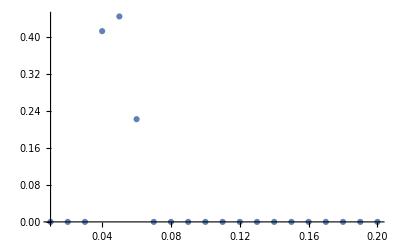

aa = 0.1

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

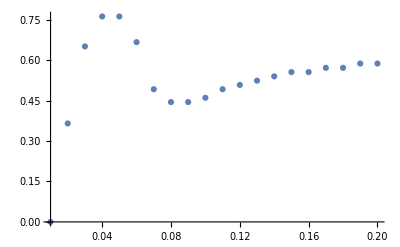

aa = 0.15

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

{t→94.2478,g→0.16,f→0.001}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

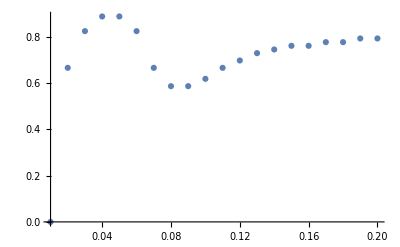

aa = 0.2

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

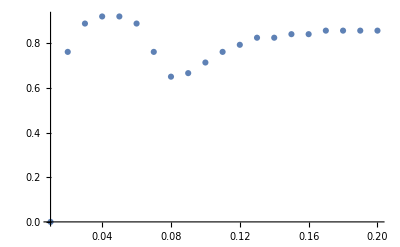

aa = 0.25

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

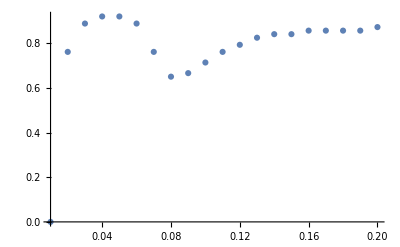

aa = 0.3

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

$Aborted

```mathematica
valuesForVariousA = {};
plotsForVariousA2={};
For[aa=0.05,aa≤0.3,aa=aa+0.05,
Print["aa = ", aa];
(*values=Table[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.01}];*)
p=DiscretePlot[
FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],
{gg,0.01,0.2,0.01},
Joined->False,
Filling->None
(*PlotRange->{{0,0.15},{0,1.3}}*)
(*AxesLabel->{"Value of g","θ[rad] s.t. QFI is maximal"},
PlotLegends->{"a = " <> ToString[aa]}*)
];
Print[p];
(*p=□DiscretePlot[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.001},Joined->False,Filling->None,PlotRange->{{0,0.15},{0,1.3}},AxesLabel->{"Value of g","optymalny kąt / pi"},PlotLegends->"t=1.5, a=0.05"]*);
plotsForVariousA2=Append[plotsForVariousA2,p];
(*valuesForVariousA = Append[valuesForVariousA,values];*)
];
```

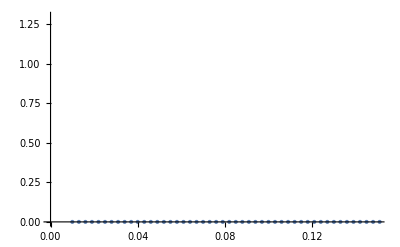

```mathematica
p
```

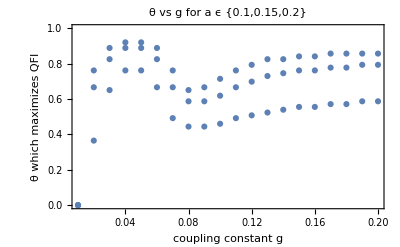

```mathematica
plotsForVariousA2;
Show[(*plotsForVariousA2[[1]],*)plotsForVariousA2[[2]],plotsForVariousA2[[3]],plotsForVariousA2[[4]],
AxesLabel->{HoldForm[coupling constant g],
HoldForm[θ which maximizes QFI]},
PlotLabel->HoldForm[θ vs g for a ϵ {0.1,0.15,0.2}],
PlotLabels->{"a=0.1","a=0.15","a=0.2"},	
Frame->{{True,False},{True,False}},
PlotRange->{0,1.0},
FrameLabel->{Style["coupling constant g"],Style["θ which maximizes QFI"]}]
```

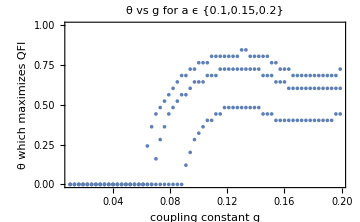

```mathematica
Show[%477,ImageSize->Medium]
```

```mathematica
plotsForVariousA2={};
multiplotList={};
For[i=0,i<3,i++,
Switch[i,
0,currentnbar=0,
1,currentnbar=1,
2,currentnbar=2];

For[aa=0.05,aa≤0.3,aa=aa+0.05,
Print["i = ", i, ", aa = ", aa];
(*values=Table[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.01}];*)
Print["Plot title will be ", "θ vs g for a ϵ {0.05`,0.1`,0.15`,0.2`}, nbar = "<> ToString[currentnbar]];
p=DiscretePlot[
FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001,nbar->currentnbar},aa,100,5],
{gg,0.01,0.2,0.003},
Joined->False,
Filling->None,
PlotRange->{{0,0.15},{0,1.3}}
(*AxesLabel->{"Value of g","θ[rad] s.t. QFI is maximal"},
PlotLegends->{"a = " <> ToString[aa]}*)
];
Print[p];
(*p=□DiscretePlot[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.001},Joined->False,Filling->None,PlotRange->{{0,0.15},{0,1.3}},AxesLabel->{"Value of g","optymalny kąt / pi"},PlotLegends->"t=1.5, a=0.05"]*);
plotsForVariousA2=Append[plotsForVariousA2,p]
(*valuesForVariousA = Append[valuesForVariousA,values];*)
];


s=Show[plotsForVariousA2[[1]],plotsForVariousA2[[2]],plotsForVariousA2[[3]],plotsForVariousA2[[4]],
AxesLabel->{HoldForm[coupling constant g],
HoldForm[θ which maximizes QFI]},
PlotLabel->"θ vs g for a ϵ {0.05`,0.1`,0.15`,0.2`}, nbar = "<> ToString[currentnbar],	
Frame->{{True,False},{True,False}},
FrameLabel->{Style["coupling constant g"],Style["θ which maximizes QFI"]}];
multiplotList=Append[multiplotList,s];
s
]
```

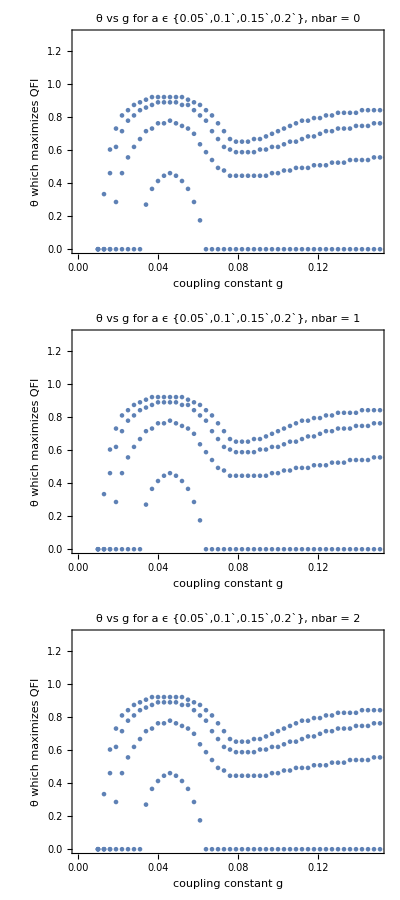
(-Graphics-)

```mathematica
multiplotList
```

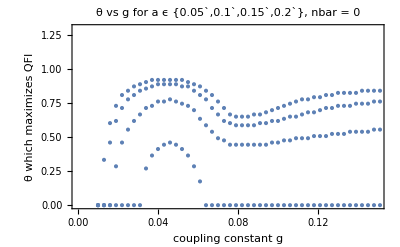

```mathematica
show1=multiplotList[[1]]
```

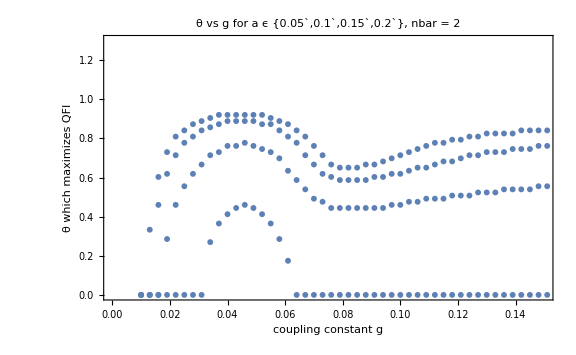

```mathematica
Show[multiplotList[[3]],ImageSize->Large]
```

### Analysis of plots in order to find optimal θ

plan minimum dajemy dekoherencje i patrzymy co sie dzieje

przechodzac do granicy chcemy odtwarzac to co oni maja do czynienia w detektorze

u nas mamy statyczne przesuniecie, a nas interesuje jak nasza amplituda sie przenosi na lustro i swiatlo
te modele prawdziwsze juz istnieją ale są robione ze swiatlem polklasycznym (tylko troche domieszki kwantowosci), a my chcemy calkiem kwantowo